# Integral transform

http://en.wikipedia.org/wiki/Integral_transform

In mathematics, an integral transform is any transform T of the following form:
(T f)(u)=(∫_t_1)^t_2 K(t,u)f(t)ⅆt
The input of this transform is a function f, and the output is another function Tf. An integral transform is a particular kind of mathematical operator.
There are numerous useful integral transforms. Each is specified by a choice of the function K of two variables, the kernel function or nucleus of the transform.
Some kernels have an associated inverse kernel K^-1(u,t) which (roughly speaking) yields an inverse transform:
f(t)=(∫_u_1)^u_2 K^-1(u,t)(T f(u))ⅆu

## Motivation

Mathematical notation aside, the motivation behind integral transforms is easy to understand. There are many classes of problems that are difficult to solve—or at least quite unwieldy algebraically—in their original representations. An integral transform “maps” an equation from its original “domain” into another domain. Manipulating and solving the equation in the target domain can be much easier than manipulation and solution in the original domain. The solution is then mapped back to the original domain with the inverse of the integral transform.

## History

The precursor of the transforms were the Fourier series to express functions in finite intervals. Later the Fourier transform was developed to remove the requirement of finite intervals.
因为级数中的各个基函数之间以参量n∈Integers来变化，这导致级数整体保留有各个基函数的周期性质。大致来说，这是因为在n为整数时，2nπ是每个三角函数的周期。所以对非周期性函数，fourier series只能在一个区间内对函数进行模拟；对周期性函数，fourier series则可以在全实数域进行模拟。
而在Fourier Transform中，n∈Reals,连续变化，这样2nπ不一定是各个基函数的周期，整体的周期性就被破坏了。
例如：对ⅇ^xfourier展开:

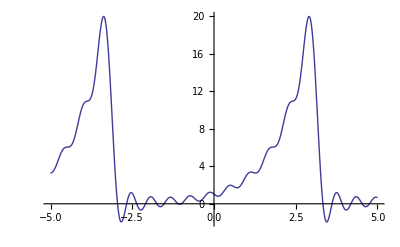

```mathematica
a=FourierSeries[E^x,x,10];b=N[a];c=Re[b];Plot[c,{x,-5,5}]
```

只在中间这个范围内是对e^x的正确模拟，这个级数本身是周期性的。

Using the Fourier series, just about any practical function of time (the voltage across the terminals of an electronic device for example) can be represented as a sum of sines and cosines, each suitably scaled (multiplied by a constant factor), shifted (advanced or retarded in time) and "squeezed" or "stretched" (increasing or decreasing the frequency). The sines and cosines in the Fourier series are an example of an orthonormal basis.

## list of Transforms

Fourier transform
Fourier sine/cosine transform
Hartley transform
Mellin transform
Laplace transform
Two-sided Laplace transform
Weierstrass transform
Hankel transform
Poisson kernel
Identity transform
N-transform

Here integral transforms are defined for functions on the real numbers, but they can be defined more generally for functions on a group.

## General theory

lthough the properties of integral transforms vary widely, they have some properties in common. For example, every integral transform is a linear operator, since the integral is a linear operator, and in fact if the kernel is allowed to be a generalized function then all linear operators are integral transforms (a properly formulated version of this statement is the Schwartz kernel theorem).
The general theory of such integral equations is known as Fredholm theory. In this theory, the kernel is understood to be a compact operator acting on a Banach space of functions. Depending on the situation, the kernel is then variously referred to as the Fredholm operator, the nuclear operator or the Fredholm kernel.